```mathematica
Copyright © 2021 Franz Utermohlen. All rights reserved.
```

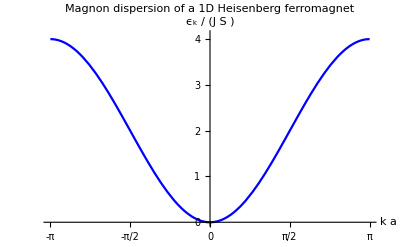

```mathematica
Plot[2(1-Cos[k]),{k,-π,π},PlotLabel->"Magnon dispersion of a 1D Heisenberg ferromagnet",LabelStyle->Directive[Black,FontSize->12],AxesLabel->{Style["k a",FontSize->14],Style[HoldForm[Subscript[ϵ, k]"/""(J S )"],FontSize->14]}, Ticks->{{-π,-π/2,0,π/2,π}, {0,1,2,3,4}},AxesStyle->Directive[Black,FontSize->12],PlotStyle->Blue,PlotRange->{Automatic,{0,4.1}}]
```

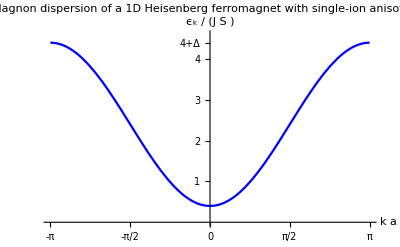

```mathematica
(*Plot[{0.2+(1-Cos[k]),2.2},{k,-π,π},PlotLabel->"Magnon dispersion of a Heisenberg ferromagnet\nwith single-ion anisotropy",LabelStyle->Directive[Black,FontSize->12],AxesLabel->{Style[HoldForm[k "/" a],FontSize->14],Style[HoldForm[ϵ[k]"/"J],FontSize->14]}, Ticks->{{-π,-π/2,0,π/2,π}, {{0.2,HoldForm[2D"/"J"     "]},0.5,1,1.5,2,{2.2,HoldForm[2+2D"/"J]}}},AxesStyle->Directive[Black,FontSize->12],PlotStyle->{Blue,{Dashed,Opacity[0.4],Gray}},PlotRange->{Automatic,{0,2.4}}]*)
Plot[0.4+2(1-Cos[k]),{k,-π,π},PlotLabel->"Magnon dispersion of a 1D Heisenberg\nferromagnet with single-ion anisotropy",LabelStyle->Directive[Black,FontSize->12],AxesLabel->{Style["k a",FontSize->14],Style[HoldForm[Subscript[ϵ, k]"/""(J S )"],FontSize->14]}, Ticks->{{-π,-π/2,0,π/2,π}, {1,2,3,4,{4.4,HoldForm[4+Δ]}}},AxesStyle->Directive[Black,FontSize->12],PlotStyle->Blue,PlotRange->{Automatic,{0,4.6}}]
```

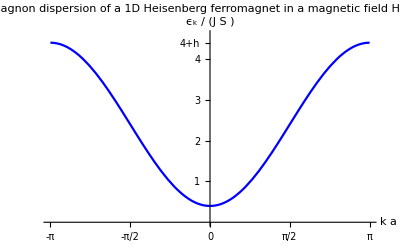

```mathematica
Plot[0.4+2(1-Cos[k]),{k,-π,π},PlotLabel->"Magnon dispersion of a 1D Heisenberg\nferromagnet in a magnetic field H = hẑ",LabelStyle->Directive[Black,FontSize->12],AxesLabel->{Style["k a",FontSize->14],Style[HoldForm[Subscript[ϵ, k]"/""(J S )"],FontSize->14]}, Ticks->{{-π,-π/2,0,π/2,π}, {1,2,3,4,{4.4,HoldForm[4+h]}}},AxesStyle->Directive[Black,FontSize->12],PlotStyle->Blue,PlotRange->{Automatic,{0,4.6}}]
```

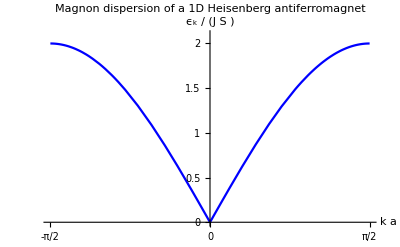

```mathematica
antiferro=Piecewise[{{2Abs[Sin[k]],Abs[k]<π/2},{Null,Abs[k]>π/2}}];
(*antiferro=2Abs[Sin[k]];*)
Plot[antiferro,{k,-π,π},PlotLabel->"Magnon dispersion of a 1D Heisenberg\nantiferromagnet",LabelStyle->Directive[Black,FontSize->12],AxesLabel->{Style["k a",FontSize->14],Style[HoldForm[Subscript[ϵ, k]"/""(J S )"],FontSize->14]}, Ticks->{{-π,-π/2,0,π/2,π}, {0,0.5,1,1.5,2}},AxesStyle->Directive[Black,FontSize->12],PlotStyle->Blue,PlotRange->{Automatic,{0,2.1}}]
```

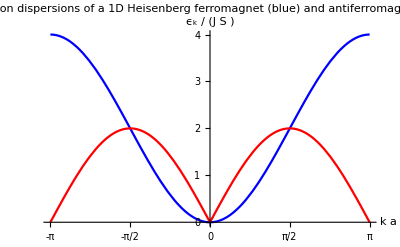

```mathematica
(*antiferro=Piecewise[{{2Abs[Sin[k]],Abs[k]<π/2},{Null,Abs[k]>π/2}}];*)
antiferro=2Abs[Sin[k]];
Plot[{2(1-Cos[k]),antiferro},{k,-π,π},PlotLabel->"Magnon dispersions of a 1D Heisenberg\nferromagnet (blue) and antiferromagnet (red)",LabelStyle->Directive[Black,FontSize->12],AxesLabel->{Style["k a",FontSize->14],Style[HoldForm[Subscript[ϵ, k]"/""(J S )"],FontSize->14]}, Ticks->{{-π,-π/2,0,π/2,π}, {0,1,2,3,4}},AxesStyle->Directive[Black,FontSize->12],PlotStyle->{Blue,Red}(*,PlotRange->{Automatic,{0,4.1}},PlotLegends->{Ferromagnet,Antferromagnet}*)]
```

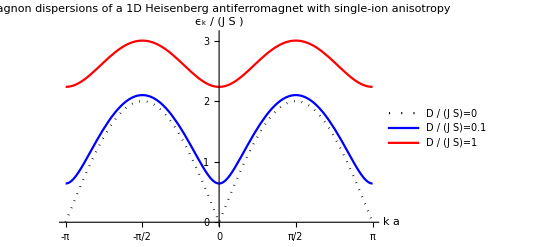

```mathematica
J=1;
Plot[{(2J+d)Sqrt[1-4(J/(2J+d) Cos[k])^2]/.d->0.0,(2J+d)Sqrt[1-4(J/(2J+d) Cos[k])^2]/.d->0.1,(2J+d)Sqrt[1-4(J/(2J+d) Cos[k])^2]/.d->1},{k,-π,π},PlotLabel->"Magnon dispersions of a 1D Heisenberg\nantiferromagnet with single-ion anisotropy",LabelStyle->Directive[Black,FontSize->12],AxesLabel->{Style["k a",FontSize->14],Style[HoldForm[Subscript[ϵ, k]"/""(J S )"],FontSize->14]}, Ticks->{{-π,-π/2,0,π/2,π}, {0,1,2,3,4}},AxesStyle->Directive[Black,FontSize->12],PlotStyle->{{Black,Dotted},Blue,Red},PlotRange->{Automatic,{0,3.1}},PlotLegends->{HoldForm[D"/""(J S)"=0],HoldForm[D"/""(J S)"=0.1],HoldForm[D"/""(J S)"=1]}]
```